# First look at lists

```mathematica
List[1,2,3,4,5]
```

{1,2,3,4,5}

```mathematica
k = List[1,2,3,4,5]
```

{1,2,3,4,5}

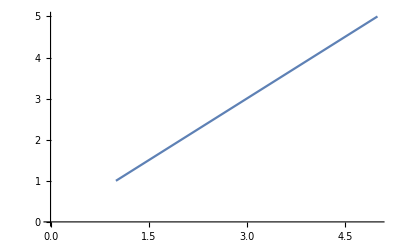

```mathematica
ListLinePlot[k]
```

```mathematica
k = {2,7,4,23,1,0,32}
```

{2,7,4,23,1,0,32}

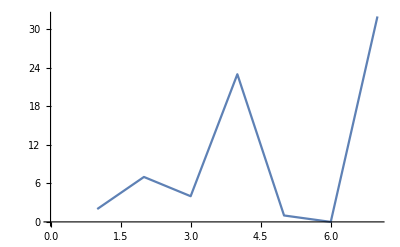

```mathematica
ListLinePlot[k]
```

```mathematica
Reverse[k]
```

{32,0,1,23,4,7,2}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

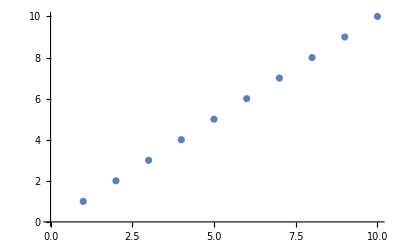

```mathematica
ListPlot[Range[10]]
```

```mathematica
k1 = List[1,2,3,4,5]
```

{1,2,3,4,5}

```mathematica
k2  = List[6,7,8,9,10]
```

{6,7,8,9,10}

```mathematica
Join[k1,k2]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Join[Range[5],Range[3]]
```

{1,2,3,4,5,1,2,3}

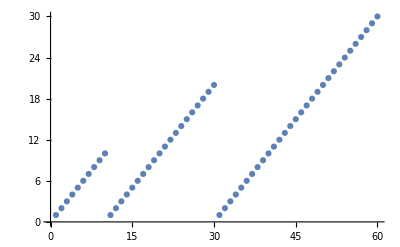

```mathematica
ListPlot[Join[Range[10],Range[20],Range[30]]]
```

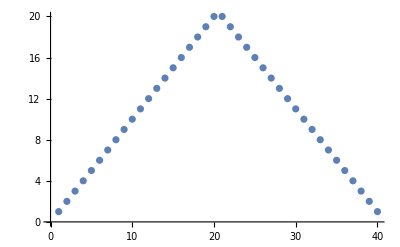

```mathematica
ListPlot[Join[Range[20],Reverse[Range[20]]]]
```

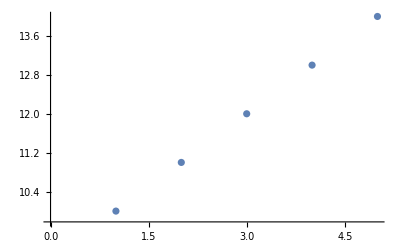

```mathematica
ListPlot[{10,11,12,13,14}]
```

# Displaying Lists

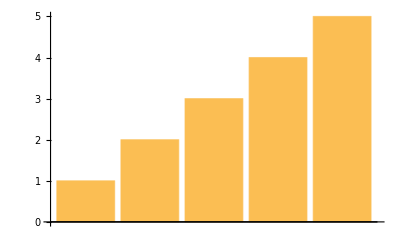

```mathematica
BarChart[k1]
```

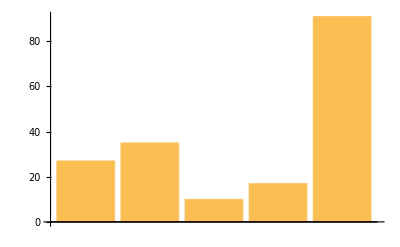

```mathematica
BarChart[{27,35,10,17,91}]
```

```mathematica
PieChart[{1,3,5,4}]
```

-Graphics-

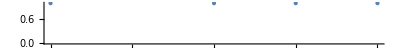

```mathematica
NumberLinePlot[{1,3,5,4}]
```

WolframAlphaQueryResults

{3.3×10^23 kg,4.867×10^24 kg,5.97×10^24 kg,6.417×10^23 kg,1.898×10^27 kg,5.683×10^26 kg,8.681×10^25 kg,1.024×10^26 kg}

WolframAlphaQueryNoResults

WolframAlphaQueryNoResults

WolframAlphaQueryNoResults

PieChart::ldata: Null is not a valid dataset or list of datasets.

PieChart[Null]

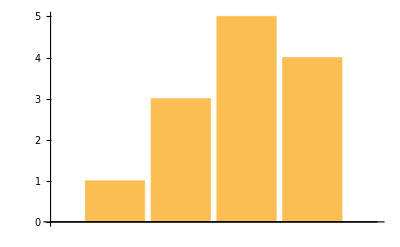
{-Graphics-,-Graphics-}

```mathematica
{PieChart[{1,3,5,4}],BarChart[{1,3,5,4}]}
```

```mathematica
Column[PieChart[{1}],PieChart[{1,1}],PieChart[{1,1,1}]]
```

Column[-Graphics-,-Graphics-,-Graphics-]

```mathematica
Column[PieChart[{1}],PieChart[{1,1}],PieChart[{1,1,1}]]
```

Column[-Graphics-,-Graphics-,-Graphics-]

```mathematica
ColumnAlignments[PieChart[{1}],PieChart[{1,1}],PieChart[{1,1,1}]]
```

ColumnAlignments[-Graphics-,-Graphics-,-Graphics-]

```mathematica
Column[{PieChart[{1}],PieChart[{1,1}],PieChart[{1,1,1}]}]
```

-Graphics-

{1,2,3,4,5,6,7,8,9,10}

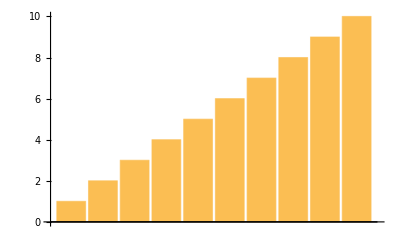
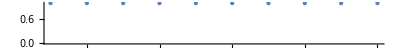
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
k=Range[10]
List[PieChart[k],BarChart[k],NumberLinePlot[k]]
```

```mathematica
1/Range[2,5]
```

{1/2,1/3,1/4,1/5}

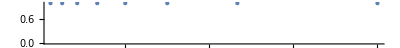

```mathematica
NumberLinePlot[1/Range[2,9]]
```

# Operations on List

```mathematica
{1,2,3}+{1,2,3,4}
```

Thread::tdlen: Objects of unequal length in {1,2,3}+{1,2,3,4} cannot be combined.

{1,2,3}+{1,2,3,4}

```mathematica
{1,2,3}+{1,2,3}
```

{2,4,6}

```mathematica
{1,2,3}+10
```

{11,12,13}

```mathematica
Part[{6,2,5,1,0,9},3]
```

5

So, basically what this Part function does is, it fetches the value at a particular index in the list.

```mathematica
Take[{1,2,3,4,5,6},3]
```

{1,2,3}

The take command what it does is it takes the first n values of list as another sub-list, where n is the user input.  The alternative to the part function is

```mathematica
{7,6,5}[[2]]
```

6

The above statement does the same task as Part function, just we need to change the index no. within “[[]]”

```mathematica
Drop[{1,2,3,4,5,6},3]
```

{4,5,6}

The above function above basically drops the no. of elements in the list and displays all other remaining elements starting from the beginning.

```mathematica
Count[{7,4,0,1,7,2,99,24,63,7,3,9,7},7]
```

4

The count function counts the no. of occurrences of that particular element in the list.

```mathematica
IntegerDigits[1957]
```

{1,9,5,7}

The above function makes a list of all the digits of the number given.

```mathematica
Length[IntegerDigits[1957]]
```

4

The above function provides the length of the list.

```mathematica
Length["Aman"]
```

0

```mathematica
f[a_,b_]:= Power[(a+b),2]
```

```mathematica
f[3,4]
```

49

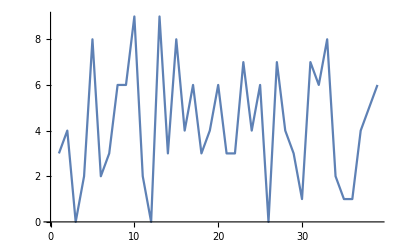

```mathematica
ListLinePlot[IntegerDigits[Power[2,128]]]
```

```mathematica
List[PieChart[IntegerDigits[Power[2,20]]],PieChart[IntegerDigits[Power[2,40]]],PieChart[IntegerDigits[Power[2,60]]]]
```

{-Graphics-,-Graphics-,-Graphics-}